## Study the wobbling quantities for 134Ce

```mathematica
ClearAll["Global`*"]
```

## 134Ce

```mathematica
ZZ=58;
AA=134;
(* fake markers *)
(* PlotMarkers->{{"△",Scaled[0.045]},{"▲",Scaled[0.07]}} *)
```

### Fitting parameters

```mathematica
A1isomer=0.03427331900399553;
A2isomer=0.022884383334125447;
A3isomer=0.014376941928523406;
A1deformed=0.031684938542074936;
A2deformed=0.021250218658037823;
A3deformed=0.011879240621271615;
bandhead=10;
```

### Theoretical formalism

```mathematica
omega[I_,A1_,A2_,A3_]:=2I*Sqrt[(A1-A3)(A2-A3)];
En[I_,n_,A1_,A2_,A3_]:=A3*I*(I+1)+omega[I,A1,A2,A3]*(n+1/2);
Exc[I_,n_,A1_,A2_,A3_]:=En[I,n,A1,A2,A3]-En[bandhead,0,A1,A2,A3];
```

### Experimental data (excitation energies)

```mathematica
spinsBand8={12,14,16,18,20};
spinsBand10={13,15,17};
spinsBand9={12,14,16,18,20,22};
spinsBand7={11,13,15};
energyBand8={0.799,1.554,2.657,3.569,4.343};
energyBand10={1.49,2.285,3.316};
energyBand9={0.464,1.188,2.005,2.878,3.862,4.864};
energyBand7={0.665,1.205,1.998};
```

### Graphical representations

#### Excitation Energies - Isomer

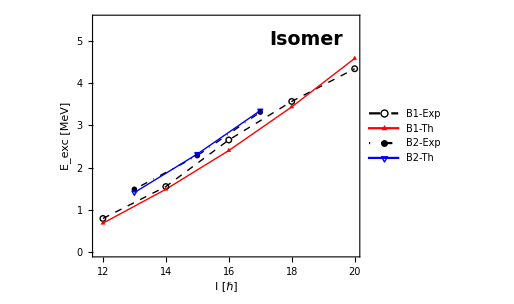

```mathematica
band8dataExp=Table[{spinsBand8[[i]],energyBand8[[i]]},{i,1,Length[spinsBand8]}];
band8dataTh=Table[{spinsBand8[[i]],Exc[spinsBand8[[i]],0,A1isomer,A2isomer,A3isomer]},{i,1,Length[spinsBand8]}];
band10dataExp=Table[{spinsBand10[[i]],energyBand10[[i]]},{i,1,Length[spinsBand10]}];
band10dataTh=Table[{spinsBand10[[i]],Exc[spinsBand10[[i]],1,A1isomer,A2isomer,A3isomer]},{i,1,Length[spinsBand10]}];
p1=ListPlot[{band8dataExp,band8dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"○",Scaled[0.045]},{"▲",Scaled[0.07]}},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},PlotRange->{Automatic,{0,5.5}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"},PlotLegends->Placed[{"B1-Exp","B1-Th"},{0.3,0.8}],Epilog->{ Inset[Style["Isomer",19,Bold,Black,Italic,FontFamily->"Times"],Scaled[{0.8,0.9}]]}];
p2=ListPlot[{band10dataExp,band10dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"●",Scaled[0.045]},{"▽",Scaled[0.07]}},PlotStyle->{{Black,DotDashed,Thick},{Blue,Thick}},PlotLegends->Placed[{"B2-Exp","B2-Th"},{0.8,0.25}],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"}];
obj1=Show[p1,p2];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-excitation-isomer.pdf",obj1];
obj1
```

#### Wobbling Energies - Isomer

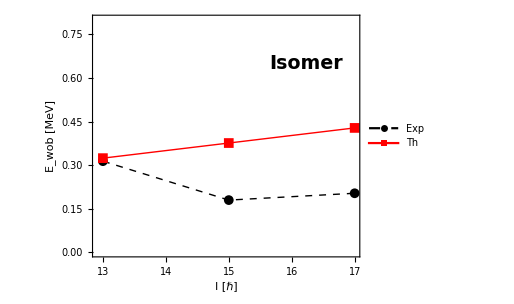

```mathematica
EwobIsomerExp=Table[{spinsBand10[[i]],energyBand10[[i]]-1/2(energyBand8[[i]]+energyBand8[[i+1]])},{i,1,Length[spinsBand10]}];
EwobIsomerTh=Table[{band10dataTh[[i,1]],band10dataTh[[i,2]]-1/2(band8dataTh[[i,2]]+band8dataTh[[i+1,2]])},{i,1,Length[band10dataTh]}];
obj2=ListPlot[{EwobIsomerExp,EwobIsomerTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp","Th"},{0.25,0.8}],FrameLabel->{"I [ℏ]","E_wob [MeV]"},Epilog->{ Inset[Style["Isomer",19,Bold,Black,Italic,FontFamily->"Times"],Scaled[{0.8,0.8}]]},PlotRange->{Automatic,{0,0.8}},PlotMarkers->{Automatic, Medium}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-wobbling-isomer.pdf",obj2];
obj2
```

#### Excitation Energies - Deformed

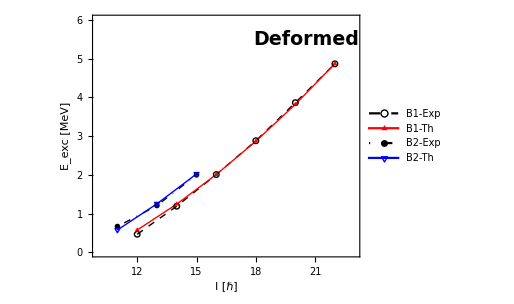

```mathematica
band9dataExp=Table[{spinsBand9[[i]],energyBand9[[i]]},{i,1,Length[spinsBand9]}];
band9dataTh=Table[{spinsBand9[[i]],Exc[spinsBand9[[i]],0,A1deformed,A2deformed,A3deformed]},{i,1,Length[spinsBand9]}];
band7dataExp=Table[{spinsBand7[[i]],energyBand7[[i]]},{i,1,Length[spinsBand7]}];
band7dataTh=Table[{spinsBand7[[i]],Exc[spinsBand7[[i]],1,A1deformed,A2deformed,A3deformed]},{i,1,Length[spinsBand7]}];
p3=ListPlot[{band9dataExp,band9dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"○",Scaled[0.045]},{"▲",Scaled[0.07]}},PlotStyle->{{Black,Dashed,Thick},{Red,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"},PlotLegends->Placed[{"B1-Exp","B1-Th"},{0.3,0.8}],PlotRange->{{10,23},{0,6}},Epilog->{ Inset[Style["Deformed",19,Bold,Black,Italic,FontFamily->"Times"],Scaled[{0.8,0.9}]]}];
p4=ListPlot[{band7dataExp,band7dataTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotMarkers->{{"●",Scaled[0.045]},{"▽",Scaled[0.07]}},PlotStyle->{{Black,DotDashed,Thick},{Blue,Thick}},PlotLegends->Placed[{"B2-Exp","B2-Th"},{0.75,0.2}],LabelStyle->{19,Bold,Black,FontFamily->"Times"},FrameLabel->{"I [ℏ]","E_exc [MeV]"}];
obj3=Show[p3,p4];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-excitation-deformed.pdf",obj3];
obj3
```

#### Wobbling Energies - Deformed

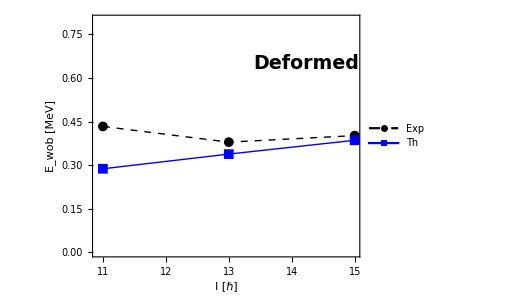

```mathematica
EwobDeformedExp=Join[{{spinsBand7[[1]],energyBand7[[1]]-1/2 energyBand9[[1]]}},Table[{spinsBand7[[i]],energyBand7[[i]]-1/2(energyBand9[[i-1]]+energyBand9[[i]])},{i,2,Length[spinsBand7]}]];
EwobDeformedTh=Join[{{spinsBand7[[1]],band7dataTh[[1,2]]-1/2 band7dataTh[[1,2]]}},Table[{spinsBand7[[i]],band7dataTh[[i,2]]-1/2(band7dataTh[[i-1,2]]+band7dataTh[[i,2]])},{i,2,Length[spinsBand7]}]];obj4=ListPlot[{EwobDeformedExp,EwobDeformedTh},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Black,Dashed,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp","Th"},{0.25,0.8}],FrameLabel->{"I [ℏ]","E_wob [MeV]"},PlotMarkers->{Automatic, Medium},Epilog->{ Inset[Style["Deformed",19,Bold,Italic,Black,FontFamily->"Times"],Scaled[{0.8,0.8}]]},PlotRange->{Automatic,{0,0.8}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-wobbling-deformed.pdf",obj4];
Show[obj4]
```

## Electromagnetic transitions

```mathematica
t1[I_,A1_,A2_,A3_]:=I(A2+A1-2A3);
t2[I_,A1_,A2_]:=I(A2-A1);
w1[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))+1))^(1/2);
w2[I_,A1_,A2_,A3_]:=(1/2(t1[I,A1,A2,A3]/(√(t1[I,A1,A2,A3]^2-t2[I,A1,A2]^2))-1))^(1/2);
Q0def[A_,Z_,beta_]:=3/(√(5π))(1.2*A^(1/3))^2*Z*beta*(1+0.16*beta);
Q20[Q0_,gm_]:=Q0*Cos[gm];
Q22[Q0_,gm_]:=1/(√2)Q0*Sin[gm];
BE2out[I_,n_,Q0_,gm_,A1_,A2_,A3_]:=5/(16π)*n/I(√3 Q20[Q0,gm]*w1[I,A1,A2,A3]+√2 Q22[Q0,gm]*w2[I,A1,A2,A3])^2;
BE2in[I_,Q0_,gm_]:=5/(16π)*Q22[Q0,gm]^2;
quench1=10^-4/2;
quench2=quench1*10;
```

## Isomer

```mathematica
gmIsomer=-35*π/180;
beta2Isomer=0.14/0.95;
w1isomer=w1[1,A1isomer,A2isomer,A3isomer];
w2isomer=w2[1,A1isomer,A2isomer,A3isomer];
Q0isomer=Q0def[AA,ZZ,beta2Isomer];
Q20isomer=Q20[Q0isomer,gmIsomer];
Q22isomer=Q22[Q0isomer,gmIsomer];
BE2inIsomer=BE2in[1,Q0isomer,gmIsomer]*quench2;
```

## Deformed

```mathematica
gmDeformed=25*π/180;
beta2Deformed=0.21/0.95;
Q0deformed=Q0def[AA,ZZ,beta2Deformed];
Q20deformed=Q20[Q0deformed,gmDeformed];
Q22deformed=Q22[Q0deformed,gmDeformed];
BE2inDeformed=BE2in[1,Q0deformed,gmDeformed]*quench2;
```

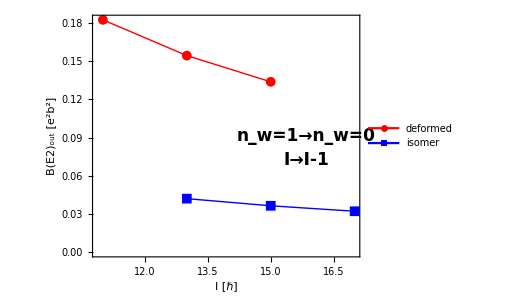

```mathematica
BE2outPlot=ListPlot[{Table[{spinsBand7[[i]],quench1*BE2out[spinsBand7[[i]],1,Q0deformed,gmDeformed,A1deformed,A2deformed,A3deformed]},{i,1,Length[spinsBand7]}],Table[{spinsBand10[[i]],quench1*BE2out[spinsBand10[[i]],1,Q0isomer,gmIsomer,A1isomer,A2isomer,A3isomer]},{i,1,Length[spinsBand10]}]},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"deformed","isomer"},{0.25,0.5}],FrameLabel->{"I [ℏ]","B(E2)_out [e^2b^2]"},PlotMarkers->{Automatic, Medium},Epilog->{Inset[Style["n_w=1→n_w=0",Bold,17,Black],Scaled[{0.8,0.5}]],Inset[Style["I→I-1",Bold,Italic,17,Black],Scaled[{0.8,0.4}]]},PlotRange->Full];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/134Ce-BE2-out.pdf",BE2outPlot];
Show[BE2outPlot]
```

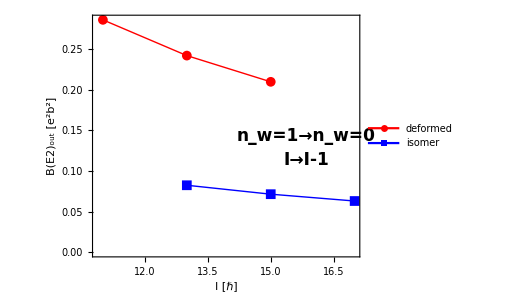

```mathematica
BE2ratio=ListPlot[{Table[{spinsBand7[[i]],(quench1*BE2out[spinsBand7[[i]],1,Q0deformed,gmDeformed,A1deformed,A2deformed,A3deformed])/BE2inDeformed},{i,1,Length[spinsBand7]}],Table[{spinsBand10[[i]],(quench1*BE2out[spinsBand10[[i]],1,Q0isomer,gmIsomer,A1isomer,A2isomer,A3isomer])/BE2inIsomer},{i,1,Length[spinsBand10]}]},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"deformed","isomer"},{0.25,0.5}],FrameLabel->{"I [ℏ]","B(E2)_out [e^2b^2]"},PlotMarkers->{Automatic, Medium},Epilog->{Inset[Style["n_w=1→n_w=0",Bold,17,Black],Scaled[{0.8,0.5}]],Inset[Style["I→I-1",Bold,Italic,17,Black],Scaled[{0.8,0.4}]]},PlotRange->Full];
Show[BE2ratio]
```

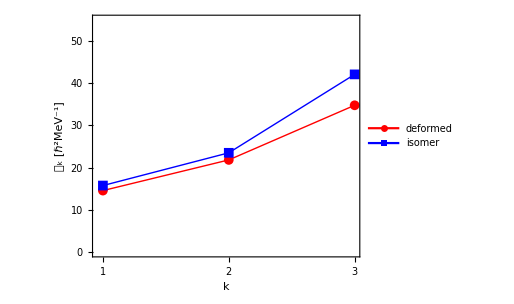

```mathematica
ListPlot[{{{1,1/(2*A1isomer)},{2,1/(2*A2isomer)},{3,1/(2A3isomer)}},{{1,1/(2A1deformed)},{2,1/(2A2deformed)},{3,1/(2A3deformed)}}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,ImageSize->380,Joined->{True, True},PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"deformed","isomer"},{0.25,0.8}],FrameLabel->{"k","𝒥_k [ℏ^2MeV^-1]"},PlotMarkers->{Automatic, Medium},PlotRange->{Automatic,{0,55}},FrameTicks->{{Automatic,None},{{1,2,3},None}}]
```